```mathematica
NotebookEvaluate[NotebookDirectory[]<>"../setup.nb"]
```

```mathematica
abortOnMessageOn[]
```

Load pre-processed data

```mathematica
Get[NotebookDirectory[]<>"../../Data/WT/mesh-data.mx"]
```

#### Angle statistics

```mathematica
angles1=With[{t=1},
Select[
vertexAngles[#,t]&/@
Select[DeleteMissing[Union[Flatten[cellVerticesTS[[t]]/@bodyCells]]],Length[vertexNeighborsTS[[t,#]]]==3&],
Total[#]>2π-0.0001&(* Exclude vertices where the angles don't sum to 2π, which happens when one of the anlges at the vertex is bigger than π *)
]
];
```

```mathematica
angles198=With[{t=198},
Select[
vertexAngles[#,t]&/@
Select[DeleteMissing[Union[Flatten[cellVerticesTS[[t]]/@bodyCells]]],Length[vertexNeighborsTS[[t,#]]]==3&],
Total[#]>2π-0.0001&
]
];//AbsoluteTiming
```

{0.944623,Null}

Render marginal angle distributions

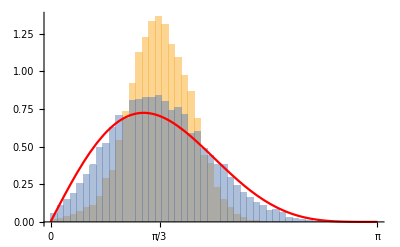

```mathematica
Show[
Histogram[{π-Flatten[angles1],π-Flatten[angles198]},{0.02π},"PDF",
PlotRange->{{0,π},Automatic},
Ticks->{{0,π/3,π},Automatic},
ChartStyle->EdgeForm[None],
PerformanceGoal->"Speed"
],
(* Marginal angle distribution in a random Delaunay triangulation *)
Plot[(4 Sin[α] ((π-α) Cos[α]+Sin[α]))/(3 π),{α,0,π},PlotStyle->Red]
]
```